# Chemical Turing Machine : Towards Universal Chemical Synthesis

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Documents/

In this section, we create a simplest example of abstract synthetic machine with architecture inspired by Turing Machine. Consider a series of chemical reactions, where R_1, R_2, R_3 are the three reagents used, P_1 and P_2 are the intermediate products, and P_3 is the final product.

R_1+R_2-> P_1+P_2
P_2 +R_3-> P_3

To perform this synthesis on an abstract synthesis machine, it requires the following process steps:
add reagent R_1
add reagent R_2
add / subtract energy (analogue variable, to be supplied externally)
add solvent S_1
separate product P_2
add reagent R_3
add / subtract energy (analogue variable, to be supplied externally)
add solvent S_2
separate product P_3

In principle we can have, an infinite tape of cells (reactors), however, if we know the total number of reagents, we need twice the number of reagents (including solvents). Each reactor on the tape can have three possible states :  0: empty reactor, 1: filled reactor, 2: active reactor. On the top of the tape, there is an active head which can perform mass transfer and hence consists of two possible states : 0: empty (no mass) and 1: full (mass). To keep the construction completely abstract and minimal, we assume the head is capable of adding and subtracting energy locally on the active reactor. As adding energy (electrochemical, photochemical, microwave, heating) and subtract energy (active cool, dissipating energy to room temperature) are usually analogue quantities, for simplicity, we make two assumptions. First, add energy and subtract energy operations occurs in pairs (as an example, heating the active reactor and once the reaction is complete, cooling it down to room temperature before performing next step). Second, as both add and subtract energy operations are analogue steps, they could have various different magnitude and time associated with them. So, add and subtract energy step could have additional attributes: {E_a, τ_a, E_r, τ_r} where E_a, E_r represent the magnitude of energy flux of addition and removing step and τ_a, τ_r are the characteristic time scales of the operation. For simplicity, we introduce energy (add and subtract) as a single step on active reactors. If a specific step only requires add energy or only subtract energy, this is equivalent to τ_a->0 or τ_r->0.

For the given reaction above, with reagent list (including solvents), {R_1, R_2, S_1, R_3, S_2}, the initialize state of the tape is:
{R_1, E, R_2, E, S_1, E, R_3, E, S_2, E}

where E are the empty reactors. We initialize the first empty reactor as active,
{R_1, A, R_2, E, S_1, E, R_3, E, S_2, E}

which can be also represented as:
{1, 2, 1, 0, 1, 0, 1, 0, 1, 0}

The head is initialized at the left most reactor (R_1) and with state 0. The rules are defined as (H is the head state, C is the tape (reactor) state)

if(C==0 && H==0) ->C=0, H=0, move RIGHT 

if(C==1 && H==0) ->C=0, H=1, move RIGHT [subtract matter]

if(C==0 && H==1) ->C=2, H=0, move LEFT  [add matter]

if(C==1 && H==1) ->C=1, H=1, move RIGHT  

if(C==2 && H==1) ->C=2, H=0, move LEFT [add matter]

if(C==2 && H==0) ->C=0, H=1, move RIGHT [add/subtract energy “react” and subtract matter]

These steps are performed until the head reaches the rightmost reactor with C==2, H==0.

```mathematica
reagentList={R1, R2, S1, R3, S2};
```

```mathematica
reagentCellStates=ConstantArray[1,Length@reagentList];
emptyCellStates=ConstantArray[0,Length@reagentList];
```

```mathematica
cellStates=Flatten@MapThread[{#1,#2}&,{reagentCellStates,emptyCellStates}];
```

```mathematica
activeCellPos=First@Flatten@Position[cellStates,0];
cellStates[[activeCellPos]]=2;
```

```mathematica
cellStates
```

{1,2,1,0,1,0,1,0,1,0}

```mathematica
initState={cellStates,0,1}
```

{{1,2,1,0,1,0,1,0,1,0},0,1}

```mathematica
Clear[operationsList];operationsList={};
```

```mathematica
ruleList[{cellStates_,cHeadState_,pos_}]:=Block[{currentcellStates=cellStates,cCellStateN,cHeadStateN,posN},
Which[
currentcellStates[[pos]]==0 && cHeadState==0,operationsList=Join[operationsList,{"-"}];
{currentcellStates[[pos]]=0,cHeadStateN=0,posN=pos+1},
currentcellStates[[pos]]==1 && cHeadState==0,operationsList=Join[operationsList,{"SM"}];
{currentcellStates[[pos]]=0,cHeadStateN=1,posN=pos+1},
currentcellStates[[pos]]==0 && cHeadState==1,operationsList=Join[operationsList,{"AM"}];
{currentcellStates[[pos]]=2,cHeadStateN=0,posN=pos-1},
currentcellStates[[pos]]==1 && cHeadState==1,operationsList=Join[operationsList,{"-"}];
{currentcellStates[[pos]]=1,cHeadStateN=1,posN=pos+1},
currentcellStates[[pos]]==2 && cHeadState==1,operationsList=Join[operationsList,{"AM"}];
{currentcellStates[[pos]]=2,cHeadStateN=0,posN=pos-1},
currentcellStates[[pos]]==2 && cHeadState==0,operationsList=Join[operationsList,{"ΔE & SM"}];
{currentcellStates[[pos]]=0,cHeadStateN=1,posN=pos+1}];
{currentcellStates,cHeadStateN,posN}]
```

```mathematica
state=initState;accumulatedStates={state};
```

```mathematica
While[state[[1]][[-1]]!=2||state[[2]]!=0||state[[3]]!=Length@state[[1]],state=ruleList[state];accumulatedStates=Join[accumulatedStates,{state}]]
```

```mathematica
MapThread[{#1,#2}&,{accumulatedStates,Flatten@{operationsList,"-"}}]//MatrixForm
```

({{1,2,1,0,1,0,1,0,1,0},0,1} | SM
{{0,2,1,0,1,0,1,0,1,0},1,2} | AM
{{0,2,1,0,1,0,1,0,1,0},0,1} | -
{{0,2,1,0,1,0,1,0,1,0},0,2} | ΔE & SM
{{0,0,1,0,1,0,1,0,1,0},1,3} | -
{{0,0,1,0,1,0,1,0,1,0},1,4} | AM
{{0,0,1,2,1,0,1,0,1,0},0,3} | SM
{{0,0,0,2,1,0,1,0,1,0},1,4} | AM
{{0,0,0,2,1,0,1,0,1,0},0,3} | -
{{0,0,0,2,1,0,1,0,1,0},0,4} | ΔE & SM
{{0,0,0,0,1,0,1,0,1,0},1,5} | -
{{0,0,0,0,1,0,1,0,1,0},1,6} | AM
{{0,0,0,0,1,2,1,0,1,0},0,5} | SM
{{0,0,0,0,0,2,1,0,1,0},1,6} | AM
{{0,0,0,0,0,2,1,0,1,0},0,5} | -
{{0,0,0,0,0,2,1,0,1,0},0,6} | ΔE & SM
{{0,0,0,0,0,0,1,0,1,0},1,7} | -
{{0,0,0,0,0,0,1,0,1,0},1,8} | AM
{{0,0,0,0,0,0,1,2,1,0},0,7} | SM
{{0,0,0,0,0,0,0,2,1,0},1,8} | AM
{{0,0,0,0,0,0,0,2,1,0},0,7} | -
{{0,0,0,0,0,0,0,2,1,0},0,8} | ΔE & SM
{{0,0,0,0,0,0,0,0,1,0},1,9} | -
{{0,0,0,0,0,0,0,0,1,0},1,10} | AM
{{0,0,0,0,0,0,0,0,1,2},0,9} | SM
{{0,0,0,0,0,0,0,0,0,2},1,10} | AM
{{0,0,0,0,0,0,0,0,0,2},0,9} | -
{{0,0,0,0,0,0,0,0,0,2},0,10} | -)

```mathematica
ArrayPlot[accumulatedStates[[All,1]],ColorRules->{0->Black,1->Red,2->Green}];
```

```mathematica
plotState=accumulatedStates[[1]];
```

```mathematica
colorRuleTape={0->LightBlue,1->LightRed,2->LightYellow};
colorRuleHead={0->Darker@Blue,1->Darker@Green};
```

```mathematica
headDirections=Flatten@{Differences@accumulatedStates[[All,3]],0};
operationsList=Flatten@{operationsList,"-"};
```

```mathematica
output=Table[Block[{plotState=accumulatedStates[[j]]},Graphics[{Table[{plotState[[1]][[i]]/.colorRuleTape,EdgeForm[Directive[White]],Rectangle[{i,0}]},{i,Length@cellStates}],Block[{pos=plotState[[3]],headstate=plotState[[2]]},{headstate/.colorRuleHead,Rectangle[{pos+0.35,0.5},{pos+0.65,0.8}],Black,Which[headDirections[[j]]==1,Arrow[{{pos+0.1,0.3},{pos+0.9,0.3}}],headDirections[[j]]==-1,Arrow[{{pos+0.9,0.4},{pos+0.1,0.4}}],headDirections[[j]]==0,Disk[{pos+0.5,0.3},0.1]]}],Text[operationsList[[j]],{Length@cellStates+5,0.5},Right]},ImageSize->200]],{j,Length@accumulatedStates}];
```

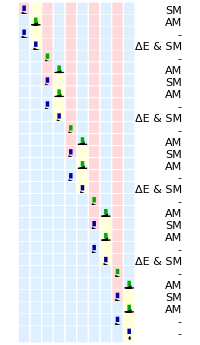

```mathematica
out=GraphicsColumn[output,Spacings->{-10,-10},ImageSize->200]
```

```mathematica
colorRuleTape
```

{0→RGBColor[0.87, 0.94, 1],1→RGBColor[1, 0.85, 0.85],2→RGBColor[1, 1, 0.85]}

```mathematica
colorRuleHead
```

{0→RGBColor[0, 0, Rational[2, 3]],1→RGBColor[0, Rational[2, 3], 0]}

```mathematica
Export[baseDirectory<>"ChemTuringOut.svg",out]
```

/Users/abhisheksharma/Documents/ChemTuringOut.svg

```mathematica
Export[baseDirectory<>"ChemTuringOut.png",out,ImageResolution->300]
```

/Users/abhisheksharma/Documents/ChemTuringOut.png

Generating State Transition Diagram: We define the head states as A and B, and the three read / write states on the reactor tape are 0,  1,  2. The head state A represents when the head empty (0) and state B represents when head is loaded with matter (1). As shown previously, the tape states 0, 1, and 2 represents empty reactor, full reactor, and active reactor states. In the figure, START state represents when the reactor tape is initialized and the head is at the left most reactor. Similarly, the HALT state represents when the reaction is finished which is when the head is empty, and the active reactor is the right most reactor. The edge labels represents: current tape state/updated tape state and action on the head (R: move right, and L: move left). In the second version of the figure (bottom), we also add operations for clarity where AM: add matter, SM: subtract matter, ΔE: add/subtract energy.

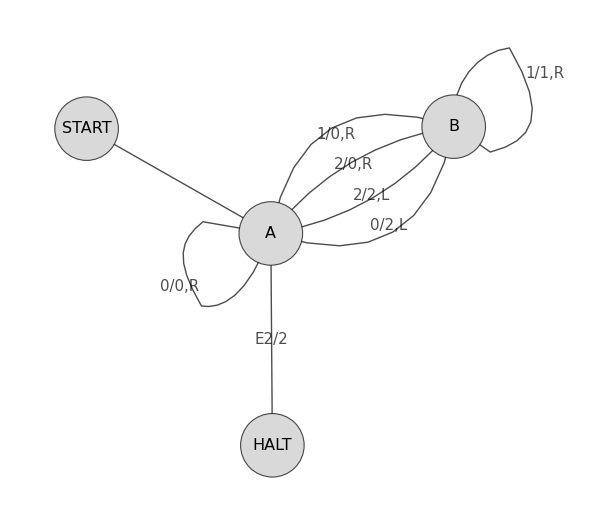

```mathematica
GraphPlot[{
Labeled["START"->"A",""],
Labeled["A"->"A","0/0,R"],
Labeled["A"->"B","1/0,R"],
Labeled["B"->"A","0/2,L"],
Labeled["B"->"B","1/1,R"],
Labeled["B"->"A","2/2,L"],
Labeled["A"->"B","2/0,R"],
Labeled["A"->"HALT","E2/2"]
},
VertexShapeFunction->(Disk[#1,0.15]&),VertexLabels->Placed["Name",Center],VertexStyle->LightGray,VertexLabelStyle->Directive[16,Black],
VertexLabels->Automatic,EdgeShapeFunction->{{"FilledArrow","ArrowSize"->0.02}},
EdgeLabelStyle->Directive[Black,15,Background->White],EdgeStyle->Black,DirectedEdges->True,MultiedgeStyle->0.5,ImageSize->600]
```

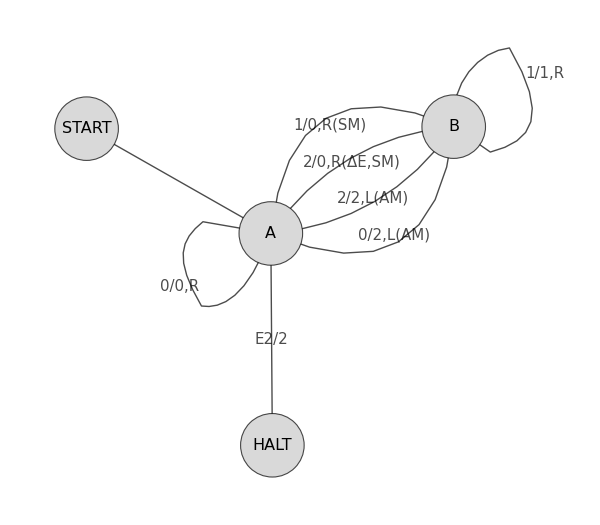

```mathematica
out=GraphPlot[{
Labeled["START"->"A",""],
Labeled["A"->"A","0/0,R"],
Labeled["A"->"B","1/0,R(SM)"],
Labeled["B"->"A","0/2,L(AM)"],
Labeled["B"->"B","1/1,R"],
Labeled["B"->"A","2/2,L(AM)"],
Labeled["A"->"B","2/0,R(ΔE,SM)"],
Labeled["A"->"HALT","E2/2"]
},
VertexShapeFunction->(Disk[#1,0.15]&),VertexLabels->Placed["Name",Center],VertexStyle->LightGray,VertexLabelStyle->Directive[16,Black],
VertexLabels->Automatic,EdgeShapeFunction->{{"FilledArrow","ArrowSize"->0.02}},
EdgeLabelStyle->Directive[Black,15,Background->White],EdgeStyle->Black,DirectedEdges->True,MultiedgeStyle->0.6,ImageSize->600]
```

```mathematica
Export[baseDirectory<>"ChemTuringOut_2.svg",out]
```

/Users/abhisheksharma/Documents/ChemTuringOut_2.svg

```mathematica
Export[baseDirectory<>"ChemTuringOut_2.png",out,ImageResolution->300]
```

/Users/abhisheksharma/Documents/ChemTuringOut_2.png